## Example 1

# Creating and plotting a pattern and its generating set

This example demonstrates, how to compute all points belonging to a pattern 𝒫(M) and how to plot them in different ways.

Author: 		Ronny Bergmann
Created: 		15.08.2013
Last Changed: 	15.08.2013

#### License

This file is part of MPAWL.
  
      MPAWL is free software : you can redistribute it and/or modify
    it under the terms of the GNU General Public License as published by
    the Free Software Foundation, either version 3 of the License, or
    (at your option) any later version.
  
      MPAWL is distributed in the hope that it will be useful,
    but WITHOUT ANY WARRANTY; without even the implied warranty of
    MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
    GNU General Public License for more details.
  
      You should have received a copy of the GNU General Public License
    along with the MPAWL. If not, see <http://www.gnu.org/licenses/>.

### Loading the Library

The MPAWL is located in the parent directory (see MPAWL.m) in order to load the library, we add its path to $Path.

```mathematica
$Path = Join[$Path,{ParentDirectory[NotebookDirectory[]]}];
SetDirectory[NotebookDirectory[]];(*Set to actual directory*)
Needs["MPAWL`"];
```

### Looking at a pattern

For a given matrix, e.g.

```mathematica
mM = {{32,4},{-1,8}}; MatrixForm[mM]
```

(32 | 4
-1 | 8)

we obtain the pattern by using the function

```mathematica
?pattern
```

pattern[mM]

generates the set of points inside the unit cube, whose multiplication with mM
results in an integral vector. The matrix mM must be in pattern normal form for
this fast algorithm to work, see getPatternNromalform[].

Options
Target →  “Unit” | “Symmetric”
	target domain of the modulus, eiter the unit cube or the unit cube shifted
	by -1/2.
validateMatrix → True | False
	whether to perform a check (via isMatrixValid[mM]) on the matrix mM.

```mathematica
?getPatternNormalform
```

getPatternNormalform[mM]

Return the normal form of the matrix mM, that generates the same pattern, i.e.
the corresponding matrix is in upper triangular form and the dominant value is
on the diagonal.

Options
validateMatrix → True | False
	whether to perform a check (via isMatrixValid[mM]) on the matrix mM.

```mathematica
patPts = pattern[getPatternNormalform[mM], Target-> "Symmetric"];
```

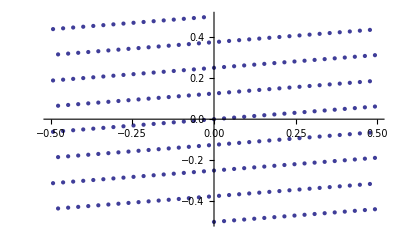

```mathematica
ListPlot[patPts, PlotRange-> {{-1/2,1/2},{-1/2,1/2}}, PlotRangePadding->0.05]
```

The rank of this lattice is given by

```mathematica
patternDimension[mM]
```

1

, i.e. we only need one vector, that spans these points by its integral scales, this vector is e.g.

```mathematica
{v} = patternBasis[mM]
```

{{2/65,1/260}}

The Smith form also provides the set of scalars, a*v, a=0,...,ϵ, such that these are the pattern (when using modulo 1 or the shifted modulo operation for the symmetric case)

```mathematica
IntegerSmithForm[mM, ExtendedForm-> False] //MatrixForm
```

(1 | 0
0 | 260)

```mathematica
ϵ = IntegerSmithForm[mM, ExtendedForm-> False][[2,2]]
```

260

So the pattern can also be given by using modM[] and this one vector, i.e.

```mathematica
?modM
```

modM[k, mM]

calculates the modulus of k with respect to the matrix mM, i.e. the vector h
in the unit cube such that k = h + mM*z.

Options

Target →  “Unit” | “Symmetric”
	target domain of the modulus, eiter the unit cube or the unit cube shifted
	by -1/2.

validateMatrix → True | False
	whether to perform a check (via isMatrixValid[mM]) on the matrix mM.

```mathematica
ListPlot[Table[modM[k*v,IdentityMatrix[2],Target-> "Symmetric"],{k,0,ϵ-1} ], PlotRange-> {{-1/2,1/2},{-1/2,1/2}}, PlotRangePadding->0.05]
```

-Graphics-

Finally, another possibility to look at a pattern is, to plot it on a torus. This emphasizes the fact, that all additions in the application are seen modulo 1, which is the same as "running around" on the torus.

```mathematica
plotOnTorus[mM]
```

-Graphics3D-

### The corresponding generating set

The generating set the MPAW Library work with, is the one of Transpose[mM]. We can also plot this, but now we really need the usual matrix (not its pattern normal form) to obtain the generating set

```mathematica
?generatingSet
```

generatingSet[mM]

Returns the set of integer vectors originalting from the corresponding
pattern[mM] by multiplying each element with mM.

Options

Target →  “Unit” | “Symmetric”
	target domain of the modulus, eiter the unit cube or the unit cube shifted
	by -1/2.

validateMatrix → True | False
	whether to perform a check (via isMatrixValid[mM]) on the matrix mM.

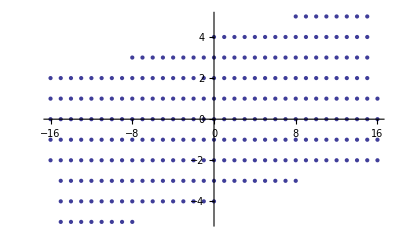

```mathematica
ListPlot[generatingSet[Transpose[mM], Target-> "Symmetric"]]
```

Here, this set is also given as the scalar multiplicities of the same number of vectors as for the pattern above, i.e. the one vector

```mathematica
{g} = generatingSetBasis[Transpose[mM]]
```

{{0,1}}

```mathematica
ListPlot[Table[modM[k*g,Transpose[mM],Target-> "Symmetric"],{k,0,ϵ-1}]]
```

-Graphics-

And we further can decompose an element of the generating set into its basis vector fractions, which is here obtaining the corresponding k:

```mathematica
?generatingSetBasisDecomp
```

generatingSetBasisDecomp[k,mM]

For the standard Basis of the generating Set provided by
generatingSetBasis[mM] the (integer) Coefficients, that reconstruct x from the
basis (up to equivalence with respect to mod[k,mM].

Options

Target →  “Unit” | “Symmetric”
	target domain of the modulus, eiter the unit cube or the unit cube shifted
	by -1/2.

validateMatrix → True | False
	whether to perform a check (via isMatrixValid[mM]) on the matrix mM.

```mathematica
generatingSetBasisDecomp[{3,3},Transpose[mM],Target-> "Symmetric"]
```

{27}

```mathematica
modM[27*g,Transpose[mM], Target-> "Symmetric"]
```

{3,3}